ResourceFunction["MaTeXInstall"][]

```mathematica
<<MaTeX`
```

```mathematica
Tc=1;
```

```mathematica
f0=1;
```

```mathematica
dF[x_]:=Piecewise[{{-f0(x-Tc)^2/Tc^2,x<Tc},{0,x>Tc}}]
```

```mathematica
(**From numerics, α increases almost linearly with temperature**)
```

```mathematica
α0=0.8
```

0.8

```mathematica
α[x_,α0_]:=Piecewise[{{1-(1-α0)((Abs[x-Tc])^2/Tc^2),x<Tc},{1,x>Tc}}]
```

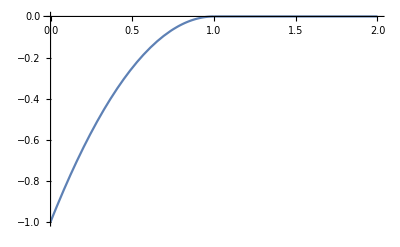

```mathematica
Plot[dF[x],{x,0,2Tc},PlotRange->All]
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
```

```mathematica
legend=SwatchLegend[{Green,Blue,Orange},{MaTeX["\\alpha_0 = 0.95",Magnification->2],MaTeX["\\alpha_0 = 0.9",Magnification->2],MaTeX["\\alpha_0 = 0.8",Magnification->2]},LegendMarkers->{Graphics[{Line[{{-1,0},{1,0}}]}]},LegendMarkerSize->25];
```

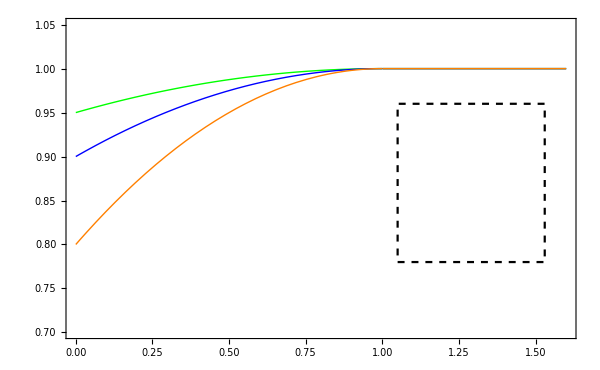

```mathematica
Legended[Show[Plot[α[x Tc,0.95],{x,0,1.6},PlotRange->{All,{0.7,1.05}},PlotStyle->{Green,Thick}],Plot[α[x Tc,0.9],{x,0,1.6},PlotRange->{All,{0.7,1.05}},PlotStyle->{Blue,Thick}],Plot[α[x Tc,0.8],{x,0,1.6},PlotRange->{All,{0.7,1.05}},PlotStyle->{Orange,Thick}],
ListPlot[{{1.05,0.78},{1.53,0.78},{1.53,0.96},{1.05,0.96},{1.05,0.78}},Joined-> True,PlotStyle-> {Black,Dashed}],
Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2],MaTeX["\\alpha(T)",Magnification->2]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,RotateLabel-> False,ImageSize->600],
Placed[legend,Scaled[{0.8,0.5}]]]
```

```mathematica
curvAvg[x_,α0_]:=(1+Exp[-dF[x]/x])/(1 + α[x,α0]Exp[-dF[x]/x])
```

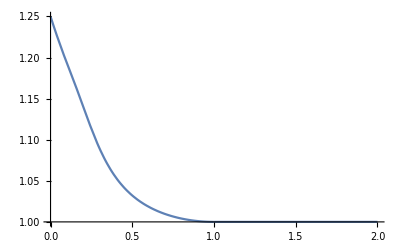

```mathematica
Plot[curvAvg[x,0.8],{x,0,2Tc},PlotRange->All]
```

```mathematica
w0 = 1;
```

```mathematica
wTBG=0.1;
```

```mathematica
w1 = 0.1;
```

```mathematica
(**Bloch-Gruneisen model**)
```

```mathematica
TBG=0.8Tc
```

0.8

```mathematica
scatteringFreqWithoutDomainTBG[x_]:=Piecewise[{{w0,x<=TBG},{w0+wTBG(x-TBG)/TBG,x>TBG}}]
```

```mathematica
(**In this model phonons contribute linearly starting at T=0**)
```

```mathematica
scatteringFreqWithoutDomainNaive[x_]:=(w0+w1 x/Tc)
```

Try w0 - w1 + w1 Sqrt[1 + x^2/TBG^2]

```mathematica
(** scatteringFreqWithDomain[x_]:=10+x+1Exp[-(x-Tc)^2/(Tc/2)^2] **)
```

```mathematica
(** scatteringFreqWithLargeDomain[x_]:=10+x+5Exp[-(x-Tc)^2/(Tc)^2] **)
```

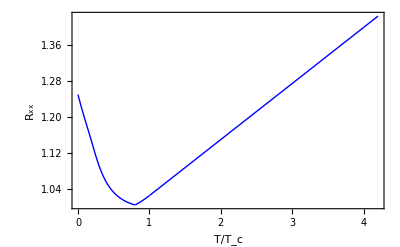

```mathematica
a1=Show[Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.8],{x,0,4.2},PlotStyle->{Blue,Thick},PlotRange->All],
FrameTicks-> {{Automatic,None},{{{0,"0"},{1,"1"},{2,"2"},{3,"3"},{4,"4"}},None}},Frame->True,FrameLabel->{"T/T_c","R_xx"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,RotateLabel-> False]
```

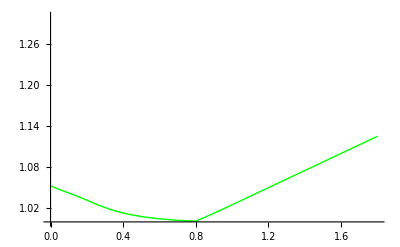

```mathematica
p1=Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.95],{x,0,1.8},PlotStyle->{Green,Thick},PlotRange->{All,{1.0,1.3}}]
```

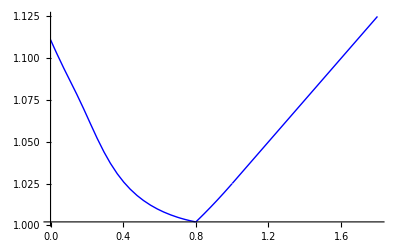

```mathematica
p2=Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.9],{x,0,1.8},PlotStyle->{Blue,Thick},PlotRange->All]
```

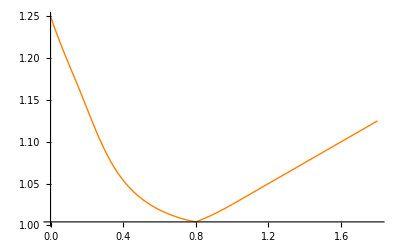

```mathematica
p3=Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.8],{x,0,1.8},PlotStyle->{Orange,Thick},PlotRange->All]
```

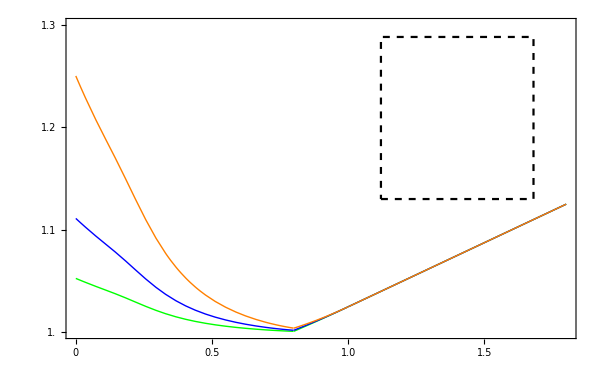

```mathematica
Legended[Show[p1,p2,p3,
ListPlot[{{1.12,1.13},{1.68,1.13},{1.68,1.288},{1.12,1.288},{1.12,1.13}},Joined-> True,PlotStyle-> {Black,Dashed}],FrameTicks-> {{{1.0,1.1,1.2,1.3},None},{{0,0.5,{1.0,"1.0"},1.5},None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2],MaTeX["\\rho_{xx}/\\rho_0",Magnification->2]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600],
Placed[legend,Scaled[{0.775,0.7}]]]
```

```mathematica
(** Plot[scatteringFreqWithDomain[x]curvAvg[x],{x,0,4Tc},PlotRange->All] **)
```

```mathematica
(** Plot[scatteringFreqWithLargeDomain[x]curvAvg[x],{x,0,4Tc},PlotRange->All]**)
```

```mathematica
(**Without the two-phase stat mech**)
```

```mathematica
a2=Plot[scatteringFreqWithoutDomain[Tc x]/α[Tc x,0.8],{x,0,4},PlotRange->All,PlotStyle->{Red}]
```

-Graphics-

```mathematica
(**Plot[scatteringFreqWithDomain[x]/α[x],{x,0,4Tc},PlotRange->All]**)
```

```mathematica
Show[a1,a2]
```

-Graphics-